```mathematica
ZR1=R1;ZR2=2*R1;ZR3=3*R1;ZR4=4*R1;ZR5=R1; ZC1=1/(s*C1);ZL1=s*L1;
```

```mathematica
ZC1L1 = ZC1*ZL1/(ZC1+ZL1);
```

```mathematica
ZC1L1R5 = ZR5+ZC1L1;
```

```mathematica
Clear[Uy, Ux]
```

```mathematica
Solve[ZR2*Uy*(1/ZR3+1/ZR2)*(1/ZR1+1/ZC1L1R5+1/ZR2)==Ux/ZR1+Uy/ZR2, Uy]
```

{{Uy→(3 (R1+L1 s+C1 L1 R1 s^2) Ux)/(11 R1+6 L1 s+11 C1 L1 R1 s^2)}}

```mathematica
Uy=(3 (R1+L1 s+C1 L1 R1 s^2) Ux)/(11 R1+6 L1 s+11 C1 L1 R1 s^2);
```

```mathematica
Ua = ZR2*Uy*(1/ZR3+1/ZR2)
```

(5 (R1+L1 s+C1 L1 R1 s^2) Ux)/(11 R1+6 L1 s+11 C1 L1 R1 s^2)

```mathematica
(*Спосіб бардіана*)
```

```mathematica
A= {{1/ZR1+1/ZC1L1+1ZR2, -1/ZR1,-1/ZR2,-1/ZC1L1},
{-1/ZR2, 0, 1/ZR2+1/ZR3,0},
{-1/ZC1L1, 0, -1/ZR3, 1/ZC1L1+1/ZR5+1/ZR4+1/ZR3}};
B = {0,0,0};
MatrixForm[A]
```

(1/R1+2 R1+(C1 (1/(C1 s)+L1 s))/L1 | -1/R1 | -1/(2 R1) | -(C1 (1/(C1 s)+L1 s))/L1
-1/(2 R1) | 0 | 5/(6 R1) | 0
-(C1 (1/(C1 s)+L1 s))/L1 | 0 | -1/(3 R1) | 19/(12 R1)+(C1 (1/(C1 s)+L1 s))/L1)

```mathematica
LinearSolve[A, B]
```

{0,0,0,0}

```mathematica
(*Спосіб барідана пососав хуй, продовжуємо спосіб паравоза, йоу*)
```

```mathematica
UC1L1R5=Ua
```

(5 (R1+L1 s+C1 L1 R1 s^2) Ux)/(11 R1+6 L1 s+11 C1 L1 R1 s^2)

```mathematica
IC1L1R5=UC1L1R5/ZC1L1R5
```

(5 (R1+L1 s+C1 L1 R1 s^2) Ux)/((11 R1+6 L1 s+11 C1 L1 R1 s^2) (R1+L1/(C1 (1/(C1 s)+L1 s))))

```mathematica
UC1L1 = IC1L1R5*ZC1L1
```

(5 L1 (R1+L1 s+C1 L1 R1 s^2) Ux)/(C1 (1/(C1 s)+L1 s) (11 R1+6 L1 s+11 C1 L1 R1 s^2) (R1+L1/(C1 (1/(C1 s)+L1 s))))

```mathematica
UC1 = Simplify[UC1L1]
```

(5 L1 s Ux)/(6 L1 s+11 R1 (1+C1 L1 s^2))

```mathematica
IL1 = UC1/ZL1
```

(5 Ux)/(6 L1 s+11 R1 (1+C1 L1 s^2))

```mathematica
Print["Uy = ", Uy]
```

Uy = (3 (R1+L1 s+C1 L1 R1 s^2) Ux)/(11 R1+6 L1 s+11 C1 L1 R1 s^2)

```mathematica
Print["Ua = ", Ua]
```

Ua = (5 (R1+L1 s+C1 L1 R1 s^2) Ux)/(11 R1+6 L1 s+11 C1 L1 R1 s^2)

```mathematica
Print["UC1 = ", UC1]
```

UC1 = (5 L1 s Ux)/(6 L1 s+11 R1 (1+C1 L1 s^2))

```mathematica
Print["IL1 = ", IL1]
```

IL1 = (5 Ux)/(6 L1 s+11 R1 (1+C1 L1 s^2))

```mathematica
GY = Uy/Ux;
```

```mathematica
GC1 = UC1/Ux;
GC1 = (5 L1 s)/Expand[6 L1 s+11 R1 (1+C1 L1 s^2)];
```

```mathematica
GL1 = IL1/Ux;
```

```mathematica
GL1 = 5/Expand[6 L1 s+11 R1 (1+C1 L1 s^2)];
```

```mathematica
Print["Gy = ",GY]
```

Gy = (3 (R1+L1 s+C1 L1 R1 s^2))/(11 R1+6 L1 s+11 C1 L1 R1 s^2)

```mathematica
Print["Gc = ", GC1]
```

Gc = (5 L1 s)/(11 R1+6 L1 s+11 C1 L1 R1 s^2)

```mathematica
Print["GL = ", GL1]
```

GL = 5/(11 R1+6 L1 s+11 C1 L1 R1 s^2)

```mathematica
(*ПЕРЕХІДНІ ХАРАКТЕРИСТИКИ*)
```

```mathematica
Hy = GY/s;
```

```mathematica
HC1 =GC1/s;
```

```mathematica
HL1 =GL1/s;
```

```mathematica
Print["Hy = ", Hy]
```

Hy = (3 (R1+L1 s+C1 L1 R1 s^2))/(s (11 R1+6 L1 s+11 C1 L1 R1 s^2))

```mathematica
Print["Hc = ", HC1]
Print["HL = ", HL1]
```

Hc = (5 L1)/(11 R1+6 L1 s+11 C1 L1 R1 s^2)

HL = 5/(s (11 R1+6 L1 s+11 C1 L1 R1 s^2))

```mathematica
Print["Dy(s) = Dc(s) = DL(s) = ",Denominator[HL1]]
```

Dy(s) = Dc(s) = DL(s) = s (11 R1+6 L1 s+11 C1 L1 R1 s^2)

```mathematica
Print[Denominator[HL1], " = 0"]
```

s (11 R1+6 L1 s+11 C1 L1 R1 s^2) = 0

```mathematica
Solve[11 R1+6 L1 s+11 C1 L1 R1 s^2==0, s]
```

{{s→(-3 L1-√(9 L1^2-121 C1 L1 R1^2))/(11 C1 L1 R1)},{s→(-3 L1+√(9 L1^2-121 C1 L1 R1^2))/(11 C1 L1 R1)}}

```mathematica
p1 = (-3 L1-√(9 L1^2-121 C1 L1 R1^2))/(11 C1 L1 R1);
p2 = (-3 L1+√(9 L1^2-121 C1 L1 R1^2))/(11 C1 L1 R1);
p3 = 0;
```

```mathematica
L1 =0.0121*10^-3; C1 = 170.219*10^-9; R1 = 17;
```

```mathematica
Print["p1 = (-3 L1 - SqrtBox[9 SuperscriptBox[L1, 2] - 121 C1 L1 SuperscriptBox[R1, 2]])/(11 C1 L1 R1) = ", p1]
```

p1 = (-3 L1 - SqrtBox[9 SuperscriptBox[L1, 2] - 121 C1 L1 SuperscriptBox[R1, 2]])/(11 C1 L1 R1) = -94247.9-690389. ⅈ

```mathematica
Print["p2 = (-3 L1 + SqrtBox[9 SuperscriptBox[L1, 2] - 121 C1 L1 SuperscriptBox[R1, 2]])/(11 C1 L1 R1) = ", p2]
```

p2 = (-3 L1 + SqrtBox[9 SuperscriptBox[L1, 2] - 121 C1 L1 SuperscriptBox[R1, 2]])/(11 C1 L1 R1) = -94247.9+690389. ⅈ

```mathematica
Print["p3 = ", p3]
```

p3 = 0

```mathematica
Clear[L1,R1,C1]
```

```mathematica
Ds = Denominator[HL1]
```

s (11 R1+6 L1 s+11 C1 L1 R1 s^2)

```mathematica
Clear[dDh]
```

```mathematica
dDh[s_]= Expand[D[Ds,s]]
```

11 R1+12 L1 s+33 C1 L1 R1 s^2

```mathematica
Print["dD(s) = ", dDh[s]]
```

dD(s) = 11 R1+12 L1 s+33 C1 L1 R1 s^2

```mathematica
Ny[s_] = Numerator[GY]
```

3 (R1+L1 s+C1 L1 R1 s^2)

```mathematica
NL1 [s_] = Numerator[GL1]
```

5

```mathematica
NC1[s_]=Numerator[GC1]
```

5 L1 s

```mathematica
h1y=Ny[p1]/dDh[p1];
```

```mathematica
h2y=Ny[p2]/dDh[p2];h3y=Ny[p3]/dDh[p3];
```

```mathematica
h1C1=NC1[p1]/dDh[p1];h2C1=NC1[p2]/dDh[p2];h3C1=NC1[p3]/dDh[p3];
```

```mathematica
h1L1=NL1[p1]/dDh[p1];h2L1=NL1[p2]/dDh[p2];h3L1=NL1[p3]/dDh[p3];
```

```mathematica
hy=h1y*Exp[p1*t]+h2y*Exp[p2*t]+h3y*Exp[p3*t];
```

```mathematica
graphHC1=h1C1*Exp[p1*t]+h2C1*Exp[p2*t]+h3C1*Exp[p3*t];
```

```mathematica
graphHL1=h1L1*Exp[p1*t]+h2L1*Exp[p2*t]+h3L1*Exp[p3*t];
```

```mathematica
L1 =0.0121*10^-3; C1 = 170.219*10^-9; R1 = 17;
```

```mathematica
Print["(Ny (p1))/(dD (p1)) = ", h1y]
```

(Ny (p1))/(dD (p1)) = 3.90313×10^-17+0.031026 ⅈ

```mathematica
Print["(Ny (p2))/(dD (p2)) = ", h2y]
```

(Ny (p2))/(dD (p2)) = 3.90313×10^-17-0.031026 ⅈ

```mathematica
Print["(Ny (p3))/(dD (p3)) = ", h3y]
```

(Ny (p3))/(dD (p3)) = 3/11

```mathematica
Print["(Nc (p1))/(dD (p1)) = ", h1C1]
```

(Nc (p1))/(dD (p1)) = 4.15787×10^-18+0.113762 ⅈ

```mathematica
Print["(Nc (p2))/(dD (p2)) = ", h2C1]
```

(Nc (p2))/(dD (p2)) = 4.15787×10^-18-0.113762 ⅈ

```mathematica
Print["(Nc (p3))/(dD (p3)) = ", h3C1]
```

(Nc (p3))/(dD (p3)) = 0

```mathematica
Print["(NL (p1))/(dD (p1)) = ", h1L1]
```

(NL (p1))/(dD (p1)) = -0.013369-0.00182506 ⅈ

```mathematica
Print["(NL (p2))/(dD (p2)) = ", h2L1]
```

(NL (p2))/(dD (p2)) = -0.013369+0.00182506 ⅈ

```mathematica
Print["(NL (p3))/(dD (p3)) = ", h3L1]
```

(NL (p3))/(dD (p3)) = 5/187

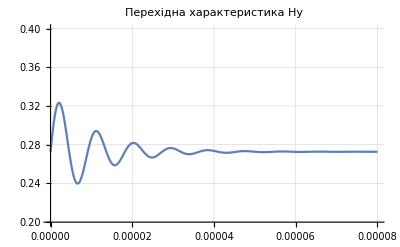

```mathematica
Plot[hy,{t,0,8*10^-5},PlotRange->{0.2,0.4},GridLines->Automatic,PlotLabel->HoldForm[Перехідна характеристика Hy]]
```

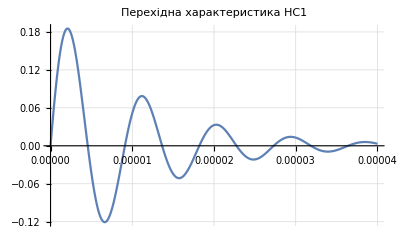

```mathematica
Plot[graphHC1,{t,0,4*10^-5},PlotRange->{0.2,-0.2},GridLines->Automatic,PlotLabel->HoldForm[Перехідна характеристика HC1]]
```

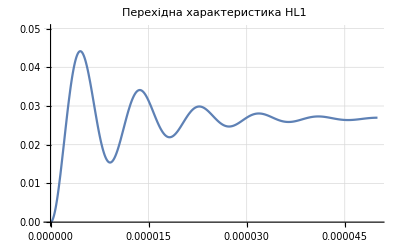

```mathematica
Plot[graphHL1,{t,0,5*10^-5},PlotRange->{0,0.05},GridLines->Automatic,PlotLabel->HoldForm[Перехідна характеристика HL1]]
```